```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="group_sn120.txt";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

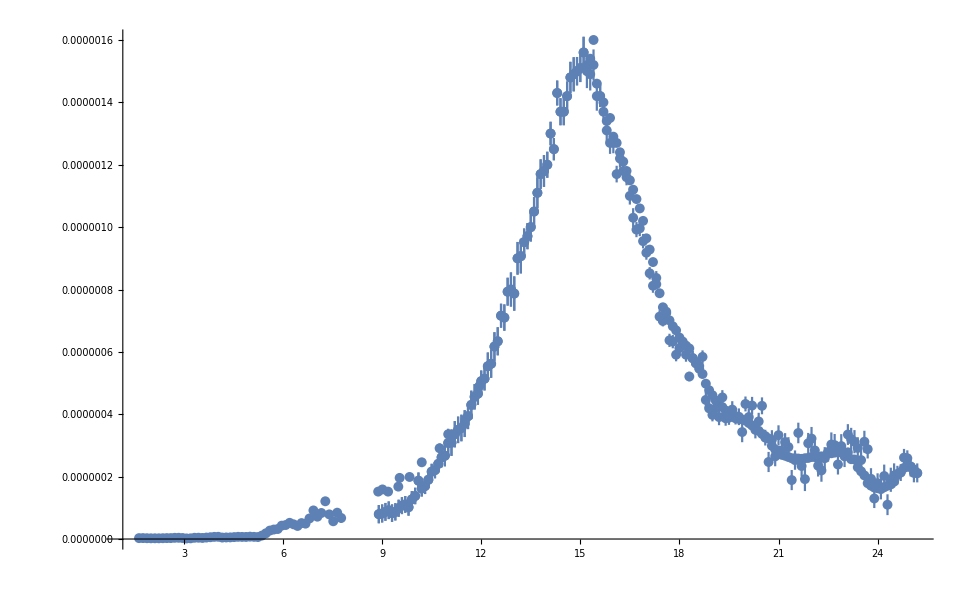

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=25.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

391

1

391

```mathematica
1
```

1

```mathematica
(*X1aver*)
```

```mathematica
(*Y1aver*)
```

```mathematica
(*dY1aver*)
```

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

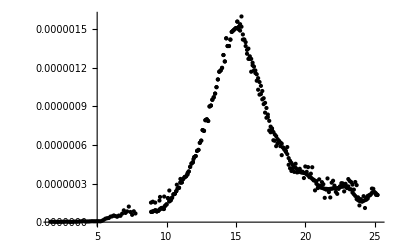

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

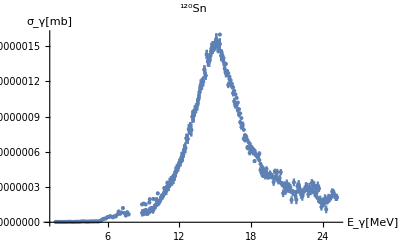

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p<17,7<omega2p<10,3<Gamma1p<6,1<Gamma2p<3,0<Gamma12p<6},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.49351×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p < 17, 7<omega2p<10, 3<Gamma1p<6, 1<Gamma2p<3, 0<Gamma12p<6 (*, Z10<10, Z20<10*)
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","120"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

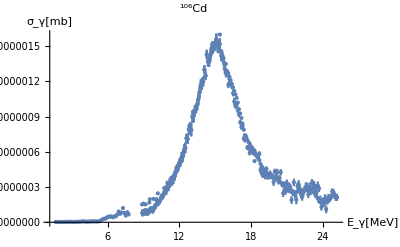

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0,10<omega1p<20},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.47668×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0, 10<omega1p < 20 },{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.49351×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.49351×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.49351×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.47668×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.47668×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2.×10^-10,1.88×10^-10,1.65×10^-10,1.75×10^-10,1.78×10^-10,1.75×10^-10,1.88×10^-10,1.59×10^-10,1.52×10^-10,1.43×10^-10,1.52×10^-10,1.61×10^-10,1.37×10^-10,1.6×10^-10,2.34×10^-10,2.33×10^-10,1.99×10^-10,2.23×10^-10,2.58×10^-10,2.79×10^-10,3.5×10^-10,2.73×10^-10,3.47×10^-10,4.75×10^-10,5.87×10^-10,5.98×10^-10,5.38×10^-10,5.6×10^-10,6.24×10^-10,6.68×10^-10,8.07×10^-10,1.02×10^-9,1.59×10^-9,2.×10^-9,2.58×10^-9,2.51×10^-9,3.49×10^-9,4.32×10^-9,5.33×10^-9,4.82×10^-9,5.07×10^-9,5.18×10^-9,5.98×10^-9,6.68×10^-9,8.54×10^-9,9.02×10^-9,1.06×10^-8,1.38×10^-8,9.82×10^-9,9.79×10^-9,1.51×10^-8,1.56×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.92×10^-8,2.89×10^-8,2.86×10^-8,2.83×10^-8,2.8×10^-8,2.77×10^-8,2.74×10^-8,2.71×10^-8,2.68×10^-8,2.71×10^-8,2.67×10^-8,2.64×10^-8,2.63×10^-8,2.57×10^-8,2.58×10^-8,2.56×10^-8,2.52×10^-8,2.63×10^-8,2.76×10^-8,3.21×10^-8,3.39×10^-8,4.34×10^-8,4.24×10^-8,4.21×10^-8,4.25×10^-8,4.26×10^-8,4.3×10^-8,4.16×10^-8,4.57×10^-8,4.07×10^-8,3.55×10^-8,3.43×10^-8,3.76×10^-8,4.4×10^-8,4.51×10^-8,4.6×10^-8,4.5×10^-8,3.84×10^-8,4.22×10^-8,4.47×10^-8,5.47×10^-8,5.5×10^-8,5.24×10^-8,5.54×10^-8,4.36×10^-8,4.19×10^-8,4.62×10^-8,4.61×10^-8,4.98×10^-8,4.73×10^-8,5.09×10^-8,4.17×10^-8,3.78×10^-8,3.57×10^-8,3.99×10^-8,4.34×10^-8,4.33×10^-8,4.69×10^-8,5.×10^-8,5.47×10^-8,4.55×10^-8,4.49×10^-8,5.03×10^-8,5.43×10^-8,5.19×10^-8,4.97×10^-8,4.68×10^-8,3.5×10^-8,3.25×10^-8,3.62×10^-8,3.52×10^-8,3.32×10^-8,2.67×10^-8,2.96×10^-8,2.37×10^-8,2.6×10^-8,2.77×10^-8,3.07×10^-8,2.43×10^-8,2.5×10^-8,2.31×10^-8,2.25×10^-8,1.98×10^-8,2.25×10^-8,2.2×10^-8,2.04×10^-8,1.73×10^-8,2.14×10^-8,2.12×10^-8,2.15×10^-8,2.12×10^-8,2.13×10^-8,2.34×10^-8,2.26×10^-8,1.5×10^-8,2.31×10^-8,2.11×10^-8,2.06×10^-8,2.08×10^-8,2.56×10^-8,2.76×10^-8,2.08×10^-8,2.09×10^-8,2.61×10^-8,2.33×10^-8,2.38×10^-8,2.3×10^-8,2.69×10^-8,2.68×10^-8,2.68×10^-8,3.26×10^-8,2.39×10^-8,2.65×10^-8,2.77×10^-8,2.74×10^-8,2.77×10^-8,2.71×10^-8,2.52×10^-8,3.23×10^-8,3.09×10^-8,3.17×10^-8,3.16×10^-8,2.67×10^-8,2.85×10^-8,3.15×10^-8,3.23×10^-8,3.1×10^-8,3.3×10^-8,3.35×10^-8,3.82×10^-8,3.32×10^-8,3.73×10^-8,3.57×10^-8,3.46×10^-8,3.63×10^-8,3.57×10^-8,3.09×10^-8,3.88×10^-8,3.57×10^-8,3.22×10^-8,3.83×10^-8,3.43×10^-8,3.33×10^-8,3.65×10^-8,3.72×10^-8,3.43×10^-8,3.39×10^-8,3.51×10^-8,2.97×10^-8,3.41×10^-8,3.07×10^-8,3.17×10^-8,3.29×10^-8,3.66×10^-8,3.34×10^-8,3.87×10^-8,3.86×10^-8,2.97×10^-8,2.69×10^-8,2.79×10^-8,2.54×10^-8,2.94×10^-8,3.02×10^-8,3.04×10^-8,9.22×10^-9,7.82×10^-9,7.54×10^-9,8.33×10^-9,1.4×10^-8,9.45×10^-9,1.38×10^-8,1.55×10^-8,1.77×10^-8,1.99×10^-8,2.51×10^-8}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][BestFitParameters]

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTable]

NonlinearModelFit[{{1.64,2.88×10^-9},{1.76,3.×10^-9},{1.88,2.58×10^-9},{2.,2.32×10^-9},{2.12,2.36×10^-9},{2.24,2.3×10^-9},{2.36,2.62×10^-9},{2.48,2.96×10^-9},{2.6,2.96×10^-9},{2.72,3.86×10^-9},{2.84,3.98×10^-9},{2.96,3.24×10^-9},{3.08,1.87×10^-9},{3.2,2.18×10^-9},{3.32,4.04×10^-9},{3.44,4.19×10^-9},{3.56,3.44×10^-9},{3.68,4.7×10^-9},{3.8,5.74×10^-9},{3.92,6.94×10^-9},{4.04,7.14×10^-9},{4.16,4.7×10^-9},{4.28,5.05×10^-9},{4.4,5.25×10^-9},{4.52,6.17×10^-9},{4.64,7.06×10^-9},{4.76,6.75×10^-9},{4.88,6.66×10^-9},{5.,7.62×10^-9},{5.12,6.98×10^-9},{5.24,6.32×10^-9},{5.36,1.1×10^-8},{5.48,1.83×10^-8},{5.6,2.71×10^-8},{5.72,3.04×10^-8},{5.84,3.21×10^-8},{5.96,4.29×10^-8},{6.08,4.49×10^-8},{6.2,5.2×10^-8},{6.32,4.71×10^-8},{6.44,4.19×10^-8},{6.56,5.11×10^-8},{6.68,4.93×10^-8},{6.8,6.59×10^-8},{6.92,9.17×10^-8},{7.04,7.16×10^-8},{7.16,8.35×10^-8},{7.28,1.21×10^-7},{7.4,7.9×10^-8},{7.52,5.69×10^-8},{7.64,8.44×10^-8},{7.76,6.74×10^-8},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.52×10^-6},{15.3,1.54×10^-6},{15.4,1.6×10^-6},{15.5,1.46×10^-6},{15.6,1.42×10^-6},{15.7,1.4×10^-6},{15.8,1.34×10^-6},{15.9,1.35×10^-6},{16.,1.29×10^-6},{16.1,1.27×10^-6},{16.2,1.24×10^-6},{16.3,1.21×10^-6},{16.4,1.18×10^-6},{16.5,1.15×10^-6},{16.6,1.12×10^-6},{16.7,1.09×10^-6},{16.8,1.06×10^-6},{16.9,1.02×10^-6},{17.,9.64×10^-7},{17.1,9.28×10^-7},{17.2,8.88×10^-7},{17.3,8.17×10^-7},{17.4,7.88×10^-7},{17.5,7.43×10^-7},{17.6,7.24×10^-7},{17.7,7.01×10^-7},{17.8,6.82×10^-7},{17.9,6.69×10^-7},{18.,6.46×10^-7},{18.1,6.33×10^-7},{18.2,6.2×10^-7},{18.3,6.11×10^-7},{18.4,5.8×10^-7},{18.5,5.67×10^-7},{18.6,5.46×10^-7},{18.7,5.29×10^-7},{18.8,4.98×10^-7},{18.9,4.77×10^-7},{19.,4.61×10^-7},{19.1,4.44×10^-7},{19.2,4.27×10^-7},{19.3,4.23×10^-7},{19.4,4.12×10^-7},{19.5,4.04×10^-7},{19.6,3.97×10^-7},{19.7,3.87×10^-7},{19.8,3.85×10^-7},{19.9,3.83×10^-7},{20.,3.8×10^-7},{20.1,3.72×10^-7},{20.2,3.64×10^-7},{20.3,3.57×10^-7},{20.4,3.47×10^-7},{20.5,3.37×10^-7},{20.6,3.3×10^-7},{20.7,3.22×10^-7},{20.8,2.99×10^-7},{20.9,2.87×10^-7},{21.,2.84×10^-7},{21.1,2.7×10^-7},{21.2,2.67×10^-7},{21.3,2.63×10^-7},{21.4,2.59×10^-7},{21.5,2.59×10^-7},{21.6,2.58×10^-7},{21.7,2.57×10^-7},{21.8,2.59×10^-7},{21.9,2.6×10^-7},{22.,2.63×10^-7},{22.1,2.63×10^-7},{22.2,2.61×10^-7},{22.3,2.65×10^-7},{22.4,2.65×10^-7},{22.5,2.74×10^-7},{22.6,2.75×10^-7},{22.7,2.77×10^-7},{22.8,2.78×10^-7},{22.9,2.78×10^-7},{23.,2.77×10^-7},{23.1,2.78×10^-7},{23.2,2.56×10^-7},{23.3,2.55×10^-7},{23.4,2.3×10^-7},{23.5,2.17×10^-7},{23.6,2.04×10^-7},{23.7,1.79×10^-7},{23.8,1.71×10^-7},{23.9,1.65×10^-7},{24.,1.63×10^-7},{24.1,1.62×10^-7},{24.2,1.66×10^-7},{24.3,1.71×10^-7},{24.4,1.75×10^-7},{24.5,1.84×10^-7},{24.6,2.09×10^-7},{24.7,2.15×10^-7},{24.8,2.28×10^-7},{24.9,2.32×10^-7},{25.,2.33×10^-7},{25.1,2.23×10^-7},{25.2,2.11×10^-7},{8.9,7.97×10^-8},{9.,8.2×10^-8},{9.1,8.7×10^-8},{9.2,9.22×10^-8},{9.3,8.3×10^-8},{9.4,8.72×10^-8},{9.5,9.86×10^-8},{9.6,1.07×10^-7},{9.7,1.11×10^-7},{9.8,1.02×10^-7},{9.9,1.27×10^-7},{10.,1.38×10^-7},{10.1,1.87×10^-7},{10.2,1.62×10^-7},{10.3,1.7×10^-7},{10.4,1.9×10^-7},{10.5,2.16×10^-7},{10.6,2.21×10^-7},{10.7,2.41×10^-7},{10.8,2.62×10^-7},{10.9,2.67×10^-7},{11.,3.08×10^-7},{11.1,3.09×10^-7},{11.2,3.36×10^-7},{11.3,3.5×10^-7},{11.4,3.56×10^-7},{11.5,3.7×10^-7},{11.6,3.94×10^-7},{11.7,4.3×10^-7},{11.8,4.56×10^-7},{11.9,4.66×10^-7},{12.,5.06×10^-7},{12.1,5.14×10^-7},{12.2,5.54×10^-7},{12.3,5.62×10^-7},{12.4,6.17×10^-7},{12.5,6.34×10^-7},{12.6,7.16×10^-7},{12.7,7.1×10^-7},{12.8,7.93×10^-7},{12.9,8.×10^-7},{13.,7.87×10^-7},{13.1,9.×10^-7},{13.2,9.07×10^-7},{13.3,9.52×10^-7},{13.4,9.71×10^-7},{13.5,1.×10^-6},{13.6,1.05×10^-6},{13.7,1.11×10^-6},{13.8,1.17×10^-6},{13.9,1.18×10^-6},{14.,1.2×10^-6},{14.1,1.3×10^-6},{14.2,1.25×10^-6},{14.3,1.43×10^-6},{14.4,1.37×10^-6},{14.5,1.37×10^-6},{14.6,1.42×10^-6},{14.7,1.48×10^-6},{14.8,1.49×10^-6},{14.9,1.5×10^-6},{15.,1.51×10^-6},{15.1,1.56×10^-6},{15.2,1.5×10^-6},{15.3,1.49×10^-6},{15.4,1.52×10^-6},{15.5,1.42×10^-6},{15.6,1.42×10^-6},{15.7,1.37×10^-6},{15.8,1.31×10^-6},{15.9,1.27×10^-6},{16.,1.27×10^-6},{16.1,1.17×10^-6},{16.2,1.22×10^-6},{16.3,1.18×10^-6},{16.4,1.16×10^-6},{16.5,1.1×10^-6},{16.6,1.03×10^-6},{16.7,9.92×10^-7},{16.8,9.96×10^-7},{16.9,9.55×10^-7},{17.,9.18×10^-7},{17.1,8.52×10^-7},{17.2,8.12×10^-7},{17.3,8.37×10^-7},{17.4,7.13×10^-7},{17.5,6.99×10^-7},{17.6,7.29×10^-7},{17.7,6.37×10^-7},{17.8,6.33×10^-7},{17.9,5.91×10^-7},{18.,6.12×10^-7},{18.1,6.28×10^-7},{18.2,5.91×10^-7},{18.3,5.21×10^-7},{18.4,5.8×10^-7},{18.5,5.63×10^-7},{18.6,5.55×10^-7},{18.7,5.84×10^-7},{18.8,4.46×10^-7},{18.9,4.19×10^-7},{19.,3.98×10^-7},{19.1,4.19×10^-7},{19.2,3.91×10^-7},{19.3,4.54×10^-7},{19.4,3.87×10^-7},{19.5,3.89×10^-7},{19.6,4.15×10^-7},{19.7,3.94×10^-7},{19.8,3.92×10^-7},{19.9,3.43×10^-7},{20.,4.33×10^-7},{20.1,3.91×10^-7},{20.2,4.28×10^-7},{20.3,3.5×10^-7},{20.4,3.77×10^-7},{20.5,4.27×10^-7},{20.6,3.25×10^-7},{20.7,2.47×10^-7},{20.8,3.18×10^-7},{20.9,2.65×10^-7},{21.,3.33×10^-7},{21.1,2.83×10^-7},{21.2,3.11×10^-7},{21.3,2.95×10^-7},{21.4,1.89×10^-7},{21.5,2.53×10^-7},{21.6,3.4×10^-7},{21.7,2.34×10^-7},{21.8,1.92×10^-7},{21.9,3.07×10^-7},{22.,3.22×10^-7},{22.1,2.84×10^-7},{22.2,2.35×10^-7},{22.3,2.2×10^-7},{22.4,2.59×10^-7},{22.5,2.79×10^-7},{22.6,3.03×10^-7},{22.7,3.01×10^-7},{22.8,2.39×10^-7},{22.9,2.98×10^-7},{23.,2.65×10^-7},{23.1,3.35×10^-7},{23.2,3.2×10^-7},{23.3,3.12×10^-7},{23.4,2.92×10^-7},{23.5,2.53×10^-7},{23.6,3.12×10^-7},{23.7,2.88×10^-7},{23.8,1.93×10^-7},{23.9,1.3×10^-7},{24.,1.79×10^-7},{24.1,1.6×10^-7},{24.2,2.02×10^-7},{24.3,1.1×10^-7},{24.4,1.9×10^-7},{24.5,2.04×10^-7},{24.6,2.05×10^-7},{24.7,2.13×10^-7},{24.8,2.61×10^-7},{24.9,2.59×10^-7},{25.,2.3×10^-7},{25.1,2.12×10^-7},{25.2,2.12×10^-7},{8.88,1.52×10^-7},{9.01,1.59×10^-7},{9.18,1.52×10^-7},{9.49,1.68×10^-7},{9.53,1.96×10^-7},{9.83,1.99×10^-7},{10.2,2.46×10^-7},{10.74,2.91×10^-7},{11.,3.36×10^-7},{11.52,3.83×10^-7},{11.94,4.9×10^-7}},{-Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.0001}},omega,Weights→{2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,5.32793×10^19,3.90625×10^19,1.82628×10^19,1.84199×10^19,2.52519×10^19,2.0109×10^19,1.50231×10^19,1.28467×10^19,8.16327×10^18,1.34176×10^19,8.30503×10^18,4.43213×10^18,2.90218×10^18,2.79639×10^18,3.4549×10^18,3.18878×10^18,2.56821×10^18,2.24103×10^18,1.53551×10^18,9.61169×10^17,3.95554×10^17,2.5×10^17,1.50231×10^17,1.58728×10^17,8.21011×10^16,5.35837×10^16,3.52002×10^16,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,4.38577×10^15,4.10914×10^15,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17283×10^15,1.1973×10^15,1.22255×10^15,1.24861×10^15,1.27551×10^15,1.30329×10^15,1.33198×10^15,1.36164×10^15,1.39229×10^15,1.36164×10^15,1.40274×10^15,1.4348×10^15,1.44573×10^15,1.51403×10^15,1.50231×10^15,1.52588×10^15,1.5747×10^15,1.44573×10^15,1.31275×10^15,9.70487×10^14,8.70163×10^14,5.3091×10^14,5.56248×10^14,5.64204×10^14,5.53633×10^14,5.51037×10^14,5.40833×10^14,5.77848×10^14,4.78815×10^14,6.03686×10^14,7.93493×10^14,8.49986×10^14,7.07334×10^14,5.16529×10^14,4.9164×10^14,4.7259×10^14,4.93827×10^14,6.78168×10^14,5.61533×10^14,5.00478×10^14,3.34215×10^14,3.30579×10^14,3.64198×10^14,3.25822×10^14,5.2605×10^14,5.69603×10^14,4.68507×10^14,4.70542×10^14,4.03219×10^14,4.46969×10^14,3.8598×10^14,5.7508×10^14,6.99868×10^14,7.84628×10^14,6.28137×10^14,5.3091×10^14,5.33365×10^14,4.54626×10^14,4.×10^14,3.34215×10^14,4.83033×10^14,4.96029×10^14,3.95243×10^14,3.39157×10^14,3.71249×10^14,4.04844×10^14,4.56571×10^14,8.16327×10^14,9.46746×10^14,7.63102×10^14,8.07076×10^14,9.07243×10^14,1.40274×10^15,1.14134×10^15,1.78034×10^15,1.47929×10^15,1.30329×10^15,1.06102×10^15,1.69351×10^15,1.6×10^15,1.87403×10^15,1.97531×10^15,2.55076×10^15,1.97531×10^15,2.06612×10^15,2.40292×10^15,3.34124×10^15,2.1836×10^15,2.22499×10^15,2.16333×10^15,2.22499×10^15,2.20415×10^15,1.82628×10^15,1.95787×10^15,4.44444×10^15,1.87403×10^15,2.24613×10^15,2.35649×10^15,2.31139×10^15,1.52588×10^15,1.31275×10^15,2.31139×10^15,2.28932×10^15,1.46798×10^15,1.84199×10^15,1.76541×10^15,1.89036×10^15,1.38196×10^15,1.39229×10^15,1.39229×10^15,9.40946×10^14,1.75067×10^15,1.42399×10^15,1.30329×10^15,1.33198×10^15,1.30329×10^15,1.36164×10^15,1.5747×10^15,9.58506×10^14,1.04733×10^15,9.95134×10^14,1.00144×10^15,1.40274×10^15,1.23115×10^15,1.00781×10^15,9.58506×10^14,1.04058×10^15,9.18274×10^14,8.91067×10^14,6.85288×10^14,9.07243×10^14,7.18757×10^14,7.84628×10^14,8.3531×10^14,7.58904×10^14,7.84628×10^14,1.04733×10^15,6.64258×10^14,7.84628×10^14,9.64469×10^14,6.81714×10^14,8.49986×10^14,9.01803×10^14,7.5061×10^14,7.22627×10^14,8.49986×10^14,8.70163×10^14,8.11682×10^14,1.13367×10^15,8.59986×10^14,1.06102×10^15,9.95134×10^14,9.23864×10^14,7.46514×10^14,8.96411×10^14,6.67695×10^14,6.71159×10^14,1.13367×10^15,1.38196×10^15,1.28467×10^15,1.55×10^15,1.15693×10^15,1.09644×10^15,1.08206×10^15,1.17635×10^16,1.63526×10^16,1.75897×10^16,1.44115×10^16,5.10204×10^15,1.11979×10^16,5.251×10^15,4.16233×10^15,3.19193×10^15,2.52519×10^15,1.58728×10^15}][ParameterTableEntries]

6.47668×10^16 FitResiduals^2

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«17»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«341» encountered.

Indeterminate

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::wts: The value of option Weights -> {2.5×10^19,2.82933×10^19,3.67309×10^19,3.26531×10^19,3.15617×10^19,3.26531×10^19,2.82933×10^19,3.95554×10^19,4.32825×10^19,4.89021×10^19,4.32825×10^19,3.85788×10^19,«27»,4.30433×10^16,3.89031×10^16,3.72684×10^16,2.79639×10^16,2.24103×10^16,1.37115×10^16,1.2291×10^16,8.89996×10^15,5.251×10^15,1.037×10^16,1.04336×10^16,«341»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

6.47668×10^16 FitResiduals^2

6.47668×10^16 FitResiduals^2

6.47668×10^16 FitResiduals^2

«1 more identical outputs»

6.49351×10^16 FitResiduals^2

6.49351×10^16 FitResiduals^2

6.49351×10^16 FitResiduals^2

«1 more identical outputs»